## Exercicício 2

## Dados

```mathematica
EI;
Len={L/4,L/2,3 L/4};
F={P,2 P,3 P}; (*forças aplicadas em x = L/4, L/2 e 3L/4, respectivamente*)
M=M1;(*momento aplicado em x = L/2*)
```

## Polinômios de Hermite: Funções de Forma

```mathematica
Pol1[x_,L_]:=x-(2*x^2/L)+(x^3/L^2) (*rotation*)
Pol2[x_,L_]:=1-(3*x^2/L^2)+(2*x^3/L^3) (*displacement*)
Pol3[x_,L_]:=-(x^2/L)+(x^3/L^2) (*rotation*)
Pol4[x_,L_]:=(3*x^2/L^2)-(2*x^3/L^3) (*displacement*)
```

## Reações de Engastamento Perfeito para Forças Pontuais

Do Teorema de Betti, tem-se que ΣFD̄ = OverBar[ΣF]D
Desenvolvendo a igualdade chega-se que, as reações resultantes de um carregamento pontual aplicado é dado por R = -F Pol(a), sendo a o ponto de aplicação da força.

### f = P

```mathematica
Mab1=F[[1]]*Pol1[L/4,L];
Print["Mab1 = ",Mab1]
Rab1=F[[1]]*Pol2[L/4,L];
Print["Rab1 = ",Rab1]
Mba1=F[[1]]*Pol3[L/4,L];
Print["Mba1 = ",Mba1]
Rba1=F[[1]]*Pol4[L/4,L];
Print["Rba1 = ",Rba1]
```

Mab1 = (9 L P)/64

Rab1 = (27 P)/32

Mba1 = -(3 L P)/64

Rba1 = (5 P)/32

### f = 2P

```mathematica
Mab2=F[[2]]*Pol1[L/2,L];
Print["Mab2 = ",Mab2]
Rab2=F[[2]]*Pol2[L/2,L];
Print["Rab2 = ",Rab2]
Mba2=F[[2]]*Pol3[L/2,L];
Print["Mba2 = ",Mba2]
Rba2=F[[2]]*Pol4[L/2,L];
Print["Rba2 = ",Rba2]
```

Mab2 = (L P)/4

Rab2 = P

Mba2 = -(L P)/4

Rba2 = P

### f = 3P

```mathematica
Mab3=F[[3]]*Pol1[3 L/4,L];
Print["Mab3 = ",Mab3]
Rab3=F[[3]]*Pol2[3 L/4,L];
Print["Rab3 = ",Rab3]
Mba3=F[[3]]*Pol3[3 L/4,L];
Print["Mba3 = ",Mba3]
Rba3=F[[3]]*Pol4[3 L/4,L];
Print["Rba3 = ",Rba3]
```

Mab3 = (9 L P)/64

Rab3 = (15 P)/32

Mba3 = -(27 L P)/64

Rba3 = (81 P)/32

## Reações de Engastamento Perfeito para Momentos Pontuais

Para os momentos, é necessário calcular a derivada dos polinômios de Hermite, já que o trabalho virtual é realizado pelo giro multiplicado pelo momento.

### m = M1

```mathematica
Mab4=M*D[Pol1[x,L],x]/.x->L/2;
Print["Mab4 = ",Mab4]
Rab4=M*D[Pol2[x,L],x]/.x->L/2;
Print["Rab4 = ",Rab4]
Mba4=M*D[Pol3[x,L],x]/.x->L/2;
Print["Mba4 = ",Mba4]
Rba4=M*D[Pol4[x,L],x]/.x->L/2;
Print["Rba4 = ",Rba4]
```

Mab4 = -M1/4

Rab4 = -(3 M1)/(2 L)

Mba4 = -M1/4

Rba4 = (3 M1)/(2 L)

## Reações de Engastamento Perfeito Totais

```mathematica
Ra=Rab1+Rab2+Rab3+Rab4;
Print["Rab = ",Ra]
Ma=Mab1+Mab2+Mab3+Mab4;
Print["Mab = ",Ma]
Rb=Rba1+Rba2+Rba3+Rba4;
Print["Rba = ",Rb]
Mb=Mba1+Mba2+Mba3+Mba4;
Print["Mba = ",Mb]
```

Rab = -(3 M1)/(2 L)+(37 P)/16

Mab = -M1/4+(17 L P)/32

Rba = (3 M1)/(2 L)+(59 P)/16

Mba = -M1/4-(23 L P)/32

## Verificação com Ftool

```mathematica
Ra/.{M1->1,P->1,L->4} //N
Rb/.{M1->1,P->1,L->4} //N
Ma/.{M1->1,P->1,L->4} //N
Mb/.{M1->1,P->1,L->4}//N
```

1.9375

4.0625

1.875

-3.125

## Derivadas dos Polinômios de Hermite

```mathematica
d1=D[x-(2*x^2/4)+(x^3/4^2),x]
d2=D[1-(3*x^2/4^2)+(2*x^3/4^3),x]
d3=D[-(x^2/4)+(x^3/4^2),x]
d4=D[(3*x^2/4^2)-(2*x^3/4^3),x]
d1/.x->2
d2/.x->2
d3/.x->2
d4/.x->2
```

1-x+(3 x^2)/16

-(3 x)/8+(3 x^2)/32

-x/2+(3 x^2)/16

(3 x)/8-(3 x^2)/32

-1/4

-3/8

-1/4

3/8

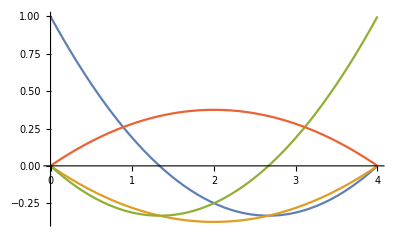

```mathematica
Plot[{d1,d2,d3,d4},{x,0,4}]
```